## 3.029 Spring 2022 Lecture 07 - 02/22/2022

## Thermodynamic Stability

Last week we talked about the fundamental thermodynamic relation

and used is in conjunction with the Legendre transform to introduce various other thermodynamic potentials

In-fact, the “natural” variables we defined for each of the thermodynamic potentials are chosen such that they minimize the thermodynamic potential

E.g. the Euler equation  is minimized for particular values of  and

## Minimum Conditions

For a function to be at a minimum:

Its first derivative must vanish

Its second derivative must be positive

```mathematica
univariateFunction[x_]=2 x^4-10 x^2+7x
```

7 x-10 x^2+2 x^4

```mathematica
univariateMinimaSols=Solve[{
univariateFunction'[x]==0,
univariateFunction''[x]>0
},x]//N
```

{{x→-1.73343},{x→1.36312}}

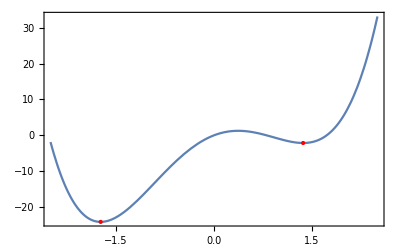

```mathematica
Plot[univariateFunction[x],{x,-5/2,5/2},Epilog->{Red,PointSize[Large],Point[{x,univariateFunction[x]}/.univariateMinimaSols]},Frame->True]
```

Note this a local minimum test

In contrast `Minimize` returns the global minimum

```mathematica
Minimize[univariateFunction[x],x]//N
```

{-24.1244,{x→-1.73343}}

For multivariate functions, a similar idea exists. 
E.g. for functions of two variables

∇_{x,y} f[x,y]={0,0}

The Hessian has to be positive-semi definite

I.e. have non-negative eigenvalues

```mathematica
hessian[f_,vars_]:=Grad[Grad[f@@vars,vars],vars]
```

```mathematica
MatrixForm[hessian[f,{x,y,z}]]
```

(f^(2,0,0)[x,y,z] | f^(1,1,0)[x,y,z] | f^(1,0,1)[x,y,z]
f^(1,1,0)[x,y,z] | f^(0,2,0)[x,y,z] | f^(0,1,1)[x,y,z]
f^(1,0,1)[x,y,z] | f^(0,1,1)[x,y,z] | f^(0,0,2)[x,y,z])

```mathematica
multivariateFunction[x_,y_]=2 x^4-10 x^2+7x y+5 y^2
```

-10 x^2+2 x^4+7 x y+5 y^2

```mathematica
multivariateMinimaSols=Solve[
Join[
Thread[Grad[multivariateFunction[x,y],{x,y}]==0],
Thread[Eigenvalues[hessian[multivariateFunction,{x,y}]]>0]
],{x,y}]//N
```

{{x→-1.76423,y→1.23496},{x→1.76423,y→-1.23496}}

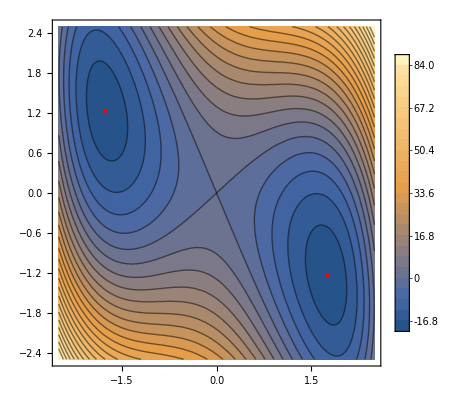

```mathematica
ContourPlot[multivariateFunction[x,y],{x,-5/2,5/2},{y,-5/2,5/2},Contours->25,Epilog->{Red,PointSize[Large],Point[{x,y}/.multivariateMinimaSols]},PlotLegends->Automatic]
```

It’s instructive to think about these using the first and second order Taylor expansions of the function

```mathematica
Simplify[Normal[Series[f[x,y],{x,x0,1},{y,y0,1}]]]/.Derivative[1,1][f][__]->0
```

f[x0,y0]+(y-y0) f^(0,1)[x0,y0]+(x-x0) f^(1,0)[x0,y0]

Which we can equivalently obtain using

```mathematica
With[{du={δx,δy}},
du.Grad[f[x,y],{x,y}]/.{x->x0,y->y0}]
```

δy f^(0,1)[x0,y0]+δx f^(1,0)[x0,y0]

Expressed in this form, the condition for a function to be at a minimum, maximum, or saddle point is given by

where the funky symbol means “for all possible choices of du”

Similarly, to second order we have

```mathematica
Simplify[Normal[Series[f[x,y],{x,x0,2},{y,y0,2}]]]/.{Derivative[2,2][f][__]->0,Derivative[1,2][f][__]->0,Derivative[2,1][f][__]->0}
```

f[x0,y0]+(y-y0) f^(0,1)[x0,y0]+1/2 (y-y0)^2 f^(0,2)[x0,y0]+(x-x0) (f^(1,0)[x0,y0]+(y-y0) f^(1,1)[x0,y0])+1/2 (x-x0)^2 f^(2,0)[x0,y0]

```mathematica
With[{du={δx,δy}},
Expand[1/2 du.hessian[f,{x,y}].du/.{x->x0,y->y0}]]
```

1/2 δy^2 f^(0,2)[x0,y0]+δx δy f^(1,1)[x0,y0]+1/2 δx^2 f^(2,0)[x0,y0]

with the condition

## Thermodynamic Stability

Back to our thermodynamic potentials

Euler’s equation suggests that there are specific values of entropy and volume which minimize the internal energy

Meaning the following form is greater than zero

I.e. the Hessian is positive semi-definite

```mathematica
MatrixForm[
hessian[U,{S,V}]
]
```

(U^(2,0)[S,V] | U^(1,1)[S,V]
U^(1,1)[S,V] | U^(0,2)[S,V])

We can use the fundamental thermodynamic relation to simplify this further by identifying

To obtain

```mathematica
MatrixForm[
internalEnergyHessian={{dtds,dtdv},{dtdv,-dpdv}}
]
```

(dtds | dtdv
dtdv | -dpdv)

```mathematica
internalEnergyStability=Reduce[Thread[Eigenvalues[internalEnergyHessian]>0],
{dpdv,dtds},Reals]
```

dpdv<0&&dtds>-dtdv^2/dpdv

In-fact, we’ve already encountered the first condition when we talked about the Van der Waals gas, and specified its bulk modulus has to be positive

Note: We used the isothermal bulk modulus, whereas we now derived a condition on the isentropic bulk modulus